Preamble for export of figures

```mathematica
<<peeters`

peeters`setGitDir["../project/figures/phy487-qmsolids"]

fs=Style[#,FontSize->14]&;
```

peeters`

/Users/pjoot/project/figures/phy487-qmsolids

Physical constants in desired units.

```mathematica
ClearAll[ physicalConstants ]
physicalConstants::usage = "Lookup of: ℏ, k_B, ...  An array of two hashes, the first with values of the quantities, the second with the names of those quantities." ;
physicalConstants = {
{
"Hbar" -> WolframAlpha["hbar in electronVolt seconds",{{"Result",1},"ComputableData"}],
"HbarSI" -> WolframAlpha["hbar in Joule seconds",{{"Result",1},"ComputableData"}],
"BoltzmannKbEvPk" -> WolframAlpha["Boltzmann constant in electronVolts per kelvin",{{"Result",1},"ComputableData"}],
"BoltzmannKbSI" -> WolframAlpha["Boltzmann constant in Joules per kelvin",{{"Result",1},"ComputableData"}],
"MassOfElectronInKg" -> WolframAlpha["mass of electron in kilograms",{{"Result",1},"ComputableData"}],
"Ge: mnStar factor" -> 0.12
},
{ 
"Hbar" -> Quantity[ "hbar" ], 
"HbarSI" -> Quantity[ "hbar" ], 
"BoltzmannKbEvPk" -> "k_B",
"BoltzmannKbSI" -> "k_B",
"MassOfElectronInKg" -> "m_e (mass of electron)",
"Ge: mnStar factor" -> "Ge: m_n^*/m_e"
}
}  ;

physicalConstants[[1]] /.physicalConstants[[2]] /. Rule->List // TableForm

Clear[pv]
pv[v_] := v/. physicalConstants[[1]] ;
```

1 | 6.582×10^-16
1 | 1.055×10^-34
k_B | 0.00008617
k_B | 1.381×10^-23
m_e (mass of electron) | 9.109×10^-31
Ge: m_n^*/m_e | 0.12

Range of N_eff^C(T)

UnitSimplify[2 (t (164.9))^(3/2)]

4235.06

2.12403×10^7

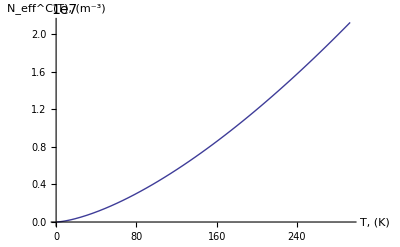

```mathematica
(* units are effectively m^(-3), but UnitSimplify fails miserably. *)
nEffC[t_] = Module[ {mnGe, h, kB},
mnGe = pv[ "Ge: mnStar factor" ] pv[ "MassOfElectronInKg" ] ;
h = 2 Pi pv[ "HbarSI" ] ;
kB =  pv[ "HbarSI" ] Quantity[1, "kelvin"];

 UnitSimplify[ 2(2 Pi mnGe kB t/h^2 )^(3/2) ]
]

nEffC[1]
nEffC[293]

Clear[p, nEffCdimensionless]
(* hack: cut and pasted the value from nEffC[1] *)
nEffCdimensionless[t_] = 4235.058618246827 t^(3/2) ;
p = Plot[ nEffCdimensionless[t], {t, 1, 293}, AxesLabel -> {"T, (K)", "N_eff^C(T), (m^-3)"}]
```

```mathematica
(*peeters`exportForLatex[ "ps10p2Fig2", p ]*)
```

Now, plot the factor in the square root: N_D/N_eff^C e^(E_d/k_BT) to get an idea of it’s range and form

```mathematica
Clear[f,eD,kB, nD, eDoverkBnonDim]
kB=pv["BoltzmannKbEvPk"]
eD=Quantity[0.0127,"eV"]
eD/kB
nD = 10^22 ;
eDoverkBnonDim = 147.38307995822208 ;
f[t_]= 4(nD/nEffCdimensionless[t]) E^(eDoverkBnonDim/ t)
Clear[p]
p = Plot[ f[t], {t, 1, 293}, AxesLabel -> {T, None}]
f[1]
f[293]
f[100]
f[1000]
```

0.00008617

0.0127

147.383

(9.44497×10^18 ⅇ^(147.383/t))/t^(3/2)

-Graphics-

9.613×10^82

3.11426×10^15

4.12361×10^16

3.46105×10^14

```mathematica
(*peeters`exportForLatex[ "ps10p2Fig3", p ]*)
```

Plot of just a linear approximation (ignoring temperature dependence of N_eff^C)

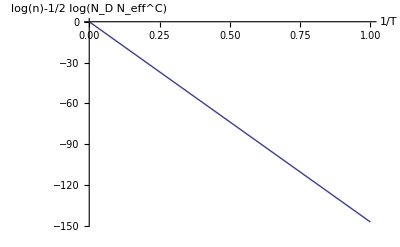

```mathematica
Clear[p]
p = Plot[
 { - eDoverkBnonDim iT}
, {iT, 1/293, 1}
, AxesLabel->{1/T, Log[n] - Log[ Subscript[N, D] Subscript[N, eff]^C]/2} 
, PlotRange->Full
]
```

Plot of the exact relation, and it’s log against temperature (not inverse temperature)

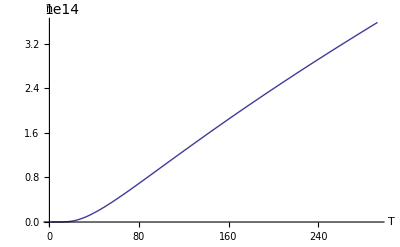

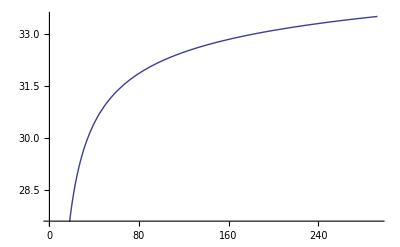

```mathematica
n[t_] = 2 nD/(1 + Sqrt[1 + f[t]]) ;
Plot[ n[t], {t, 1, 293}, AxesLabel->{T, n}]
Plot[ Log[n[t]], {t, 1, 293}]
```

Plot against inverse temperature with linear asymptote (i.e. that ignores temperature dependence of N_eff^C)

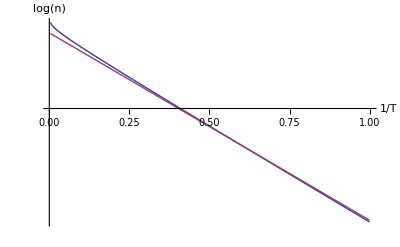

```mathematica
p = Plot[ {Log[n[1/b]], 29.475460842985516- 73 b}, {b, 1/293, 1},AxesLabel->{1/T, Log[n]}, Ticks -> {Automatic, None}]
```

Approximate numerical value of E_d/2 k_B

```mathematica
(*peeters`exportForLatex[ "ps10p2Fig1", p ]*)
```

```mathematica
eDoverkBnonDim/2
```

73.6915

The intercept

```mathematica
11Log[10]+Log[4]/2+(3/2) Log [10] // N
```

29.4755

Second inverse temperature plot requested in the problem

```mathematica
(*Plot[ 29 - 3 Log[b]/4 - 73 b, {b, 1/293, 1}]*)
```

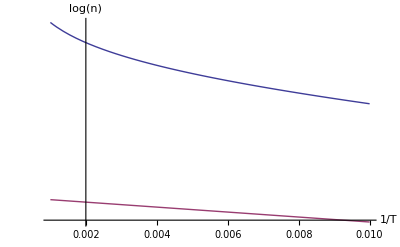

```mathematica
p = Plot[ {Log[n[1/b]], 29.475460842985516- 73 b}, {b, 1/1000, 1/100},AxesLabel->{1/T, Log[n]}, Ticks -> {Automatic, None}, PlotRange -> Full]
```

```mathematica
(*peeters`exportForLatex[ "ps10p2Fig4", p ]*)
```

```mathematica
(*p = Plot[ {Log[n[1/b]], 29.475460842985516- 73 b}, {b, 1, 1/0.01},AxesLabel->{1/T, Log[n]}, Ticks -> {Automatic, None}, PlotRange -> Full]*)
```

Numerical evaluation of the densities at a couple temperatures

```mathematica
n[1]
n[293]
n[100]
n[1000]
```

6.45061×10^-20

3.58387×10^14

9.84898×10^13

1.07504×10^15